## “NISTEP-DSlink-Target_NEW-16”

## Program

```mathematica
countNormal[list_]:=list/Tr[list]
```

```mathematica
listToSVstr[l_List]:=StringJoin[Riffle[Map[ToString,l]," "]]
```

```mathematica
toSVstrLines[l_List]:=StringJoin[Riffle[l,"\n"]]
```

```mathematica
matToSVstrLines[m_List]:=toSVstrLines[Map[listToSVstr,m]]
```

```mathematica
matTokmeansSV[m_List]:=Module[{size,mat},
size=Reverse[Dimensions[m]];
mat=Prepend[m,size];
matToSVstrLines[mat]<>"\n"
]
```

```mathematica
ColorData["NeonColors"][0]
```

RGBColor[0.720287, 0.923781, 0.297597]

## Data

```mathematica
dir="/Volumes/elecom/NII/基盤_CiNii/研究開発/ディスカバリサービス/nistep_data"
```

/Volumes/elecom/NII/基盤_CiNii/研究開発/ディスカバリサービス/nistep_data

```mathematica
SetDirectory[dir]
```

/Volumes/elecom/NII/基盤_CiNii/研究開発/ディスカバリサービス/nistep_data

```mathematica
(tsv=Import["NISTEP-DSlink-Target_New-16/services.tsv"])//Dimensions
```

{66,63}

項目名

```mathematica
tsv[[1]]
```

{,,,調査対象URL,,,,項目の説明：
階層：<数字>/<*>/<**>
<アルファベット>は「NISTEP-DSlink-Target」シートのカラム番号に相当。,1. オートコンプリート,**サジェスト,**スペルチェック,2.ベストファースト = O:ソート,* 関連度,* 人気度,* 日付,* フォーマット（ソースの）,* パーソナライズ,* 多様性（多様性(表現の多様性の吸収など)アルゴリズム）,**スコア,3. 横断検索,**エンジン（マルチエンジン）,4. ファセット型ナビ = ファセット型ナビ,L:ビルダー形式GUI,5.詳細検索 = K:詳細検索,J:検索box,6.パーソナライズ,X:login機能,**適合性のチューニング,**利用状況、利用コンテキスト,**訪問済み、履歴,**タグ、メモ、コメント,7.ページネーション = ページネーション,Q:全件表示,8. 構造化された結果（結果にふさわしい表示、Wolfram Alphaの例）,**ハイライト,**クラスタリング,**テキスト解析,V:データプロット,U:マップ,S:サムネイル,削除項目,9. アクション可能な結果（computable）,W:ロケータ/スライダ等、GUIによる指定,**パールグローイング（検索結果から次のクエリー（検索語）を導く）,N:検索結果リファイン,10. 統合的発見（システムの多機能性を利用した発見）,**レコメン,**セレンディピティ,**トピック,**曖昧性回避,11. NISTEPサービスにあるが本書にない項目（空項目）,R:バリアフリー,P:ダウンロード,M:検索対象のタイプ,T:ダウンロードのデータ形式,Y:利用統計,Z1:API,Z:その他,仕掛かり中,除外,完,担当,ジャンル}

項目範囲

```mathematica
itemStart=9
itemEnd=58
```

9

58

```mathematica
(tsvBody=Drop[tsv,2])//Dimensions
```

{64,63}

```mathematica
(tsvEvalBody=Map[#[[Range[itemStart,itemEnd]]]&,tsvBody])//Dimensions
```

{64,50}

```mathematica
(tsvEvalHead=tsv[[1]][[Range[itemStart,itemEnd]]])//Length
```

50

```mathematica
tsvEvalHead
```

{1. オートコンプリート,**サジェスト,**スペルチェック,2.ベストファースト = O:ソート,* 関連度,* 人気度,* 日付,* フォーマット（ソースの）,* パーソナライズ,* 多様性（多様性(表現の多様性の吸収など)アルゴリズム）,**スコア,3. 横断検索,**エンジン（マルチエンジン）,4. ファセット型ナビ = ファセット型ナビ,L:ビルダー形式GUI,5.詳細検索 = K:詳細検索,J:検索box,6.パーソナライズ,X:login機能,**適合性のチューニング,**利用状況、利用コンテキスト,**訪問済み、履歴,**タグ、メモ、コメント,7.ページネーション = ページネーション,Q:全件表示,8. 構造化された結果（結果にふさわしい表示、Wolfram Alphaの例）,**ハイライト,**クラスタリング,**テキスト解析,V:データプロット,U:マップ,S:サムネイル,削除項目,9. アクション可能な結果（computable）,W:ロケータ/スライダ等、GUIによる指定,**パールグローイング（検索結果から次のクエリー（検索語）を導く）,N:検索結果リファイン,10. 統合的発見（システムの多機能性を利用した発見）,**レコメン,**セレンディピティ,**トピック,**曖昧性回避,11. NISTEPサービスにあるが本書にない項目（空項目）,R:バリアフリー,P:ダウンロード,M:検索対象のタイプ,T:ダウンロードのデータ形式,Y:利用統計,Z1:API,Z:その他}

サイトID

```mathematica
tsvBodyID=Map[#[[1]]&,tsvBody]
```

{1,2,4,5,6,7,8,15,16,18,19,20,21,22,23,24,25,26,27,28,32,35,36,37,38,42,43,46,48,53,54,55,57,58,59,60,61,62,63,64,66,67,68,69,70,71,72,73,74,76,77,82,83,84,85,86,90,91,93,103,104,105,106,108}

国

```mathematica
tsvBodyNation=Map[#[[6]]&,tsvBody]
```

{日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,世界,世界,世界,世界,世界,欧州,欧州,欧州,欧州,欧州,英国,英国,英国,英国,英国,英国,オランダ,オランダ,オランダ,ドイツ,ドイツ,ドイツ,ドイツ,ドイツ,ドイツ,フランス,フランス,フランス,フランス,フランス,米国,米国,米国,米国,米国,米国,米国,米国}

```mathematica
Tally[tsvBodyNation]
```

{{日本,26},{世界,5},{欧州,5},{英国,6},{オランダ,3},{ドイツ,6},{フランス,5},{米国,8}}

ジャンル

```mathematica
tsvBodyGenre=Map[#[[-1]]&,tsvBody]
```

{経済・産業統計,経済・産業統計,学術統計,経済・産業統計,経済・産業統計,補助金情報,教育・学校統計,経済・産業調査報告,経済・産業調査報告,学術総合,学術総合,学生支援,大学情報,大学情報,学術論文,補助金情報,学術総合,経済・産業統計,特許等,経済・産業統計,経済・産業統計,学術総合,特許等,特許等,特許等,学術総合,経済・産業統計,経済・産業統計,経済・産業統計,特許等,経済・産業統計,特許等,経済・産業統計,特許等,医療健康,学術総合,学術総合,学術総合,大学情報,教育,経済・産業統計,特許等,学術統計,大学のトップページ,その他,教育,教育,補助金情報,特許等,特許等,経済・産業統計,教育,学術総合,経済・産業統計,経済・産業統計,教育・学校統計,学術総合,経済・産業統計,学術総合,学術総合,学術統計,経済・産業統計,特許等,その他}

```mathematica
Tally[tsvBodyGenre]
```

{{経済・産業統計,18},{学術統計,3},{補助金情報,3},{教育・学校統計,2},{経済・産業調査報告,2},{学術総合,12},{学生支援,1},{大学情報,3},{学術論文,1},{特許等,11},{医療健康,1},{教育,4},{大学のトップページ,1},{その他,2}}

サイト名+地域+ジャンル

```mathematica
tsvBodySite=Map[#[[7]]<>"  :"<>#[[6]]<>":"<>#[[-1]]&,tsvBody]
```

{国民経済計算  :日本:経済・産業統計,独立行政法人・国立大学法人等の科学技術関係活動に関する調査（上記と同じサイトに遷移）  :日本:経済・産業統計,科学技術研究調査  :日本:学術統計,経済センサス(上記と同じサイトに遷移)  :日本:経済・産業統計,事業所・企業統計調査（平成18年度まで）（上記と同じサイトに遷移）  :日本:経済・産業統計,科学研究費補助金　配分結果  :日本:補助金情報,国際研究交流の概況（上記と同じサイトに遷移）  :日本:教育・学校統計,科学技術システムの課題に関する代表的研究者・有識者の意識定点調査  :日本:経済・産業調査報告,全国イノベーション調査(上記と同じサイトに遷移)  :日本:経済・産業調査報告,J-GLOBAL  :日本:学術総合,researchmap  :日本:学術総合,外国人留学生在籍状況調査  :日本:学生支援,大学ポートレート  :日本:大学情報,大学基本情報  :日本:大学情報,CiNii Articles  :日本:学術論文,KAKEN  :日本:補助金情報,厚生労働科学研究成果データベース  :日本:学術総合,賃金構造基本統計調査  :日本:経済・産業統計,品種登録／出願公表データ  :日本:特許等,経済産業省企業活動基本調査  :日本:経済・産業統計,JIP (Japan Industrial Productivity) データベース  :日本:経済・産業統計,成果報告書データベース  :日本:学術総合,知的財産活動調査  :日本:特許等,特許プラットフォーム  :日本:特許等,IIPパテントデータベース  :日本:特許等,指標情報データベース  :日本:学術総合,Orbis  :世界:経済・産業統計,Main Science and Technology Indicators (MSTI)  :世界:経済・産業統計,Research &amp; Development Statistics  :世界:経済・産業統計,WIPO IP Statistics Data Center  :世界:特許等,World Bank Open Data  :世界:経済・産業統計,Espacenet  :欧州:特許等,Eurostat  :欧州:経済・産業統計,eSearch plus  :欧州:特許等,publicdata.eu  :欧州:医療健康,RISIS Datasets  :欧州:学術総合,Data.gov.uk  :英国:学術総合,Science, engineering and technology (SET) Statistics  :英国:学術総合,UNISTATS  :英国:大学情報,Finances of Higher Education Providers  :英国:教育,ONS Gross Domestic Expenditure on Research and Development  :英国:経済・産業統計,英国特許庁データベース  :英国:特許等,CWTS Leiden Ranking  :オランダ:学術統計,University-Industry Research Connections, CWTS  :オランダ:大学のトップページ,ライデン声明(Leiden manifesto for research Metrics)  :オランダ:その他,Bundesbericht Forschung und Innovation / Research and Innovation in Germany  :ドイツ:教育,Daten Potal  :ドイツ:教育,Förderatlas 2015  :ドイツ:補助金情報,DEPATISnet　ドイツ特許庁　特許検索データベース  :ドイツ:特許等,Statistiken　ドイツ特許庁統計情報（74と同じサイトになってしまう）  :ドイツ:特許等,Ausgaben, Einnahmen und Personal der öffentlichen und öffentlich geförderten Einrichtungen für Wissenschaft, Forschung und Entwicklung  :ドイツ:経済・産業統計,Evaluation Procedures  :フランス:教育,data.gouv.fr  :フランス:学術総合,Bases de données gratuites  :フランス:経済・産業統計,Statistiques structurelles d&#8217;entreprises (Alisse)  :フランス:経済・産業統計,Repères et références statistiques sur les enseignements, la formation et la recherche  :フランス:教育・学校統計,Data.gov  :米国:学術総合,National Bureau of Economic Research (NBER)  :米国:経済・産業統計,Academic Institution Profiles  :米国:学術総合,WebCASPAR  :米国:学術総合,Science and Engineering Indicators  :米国:学術統計,FedScope-Federal Human Resources Data  :米国:経済・産業統計,米国特許検索データベース  :米国:特許等,サンフランシスコ宣言(The San Francisco Declaration on Research Assessment (DORA))  :米国:その他}

## Binary Mat

```mathematica
(tsvBinaryBody=(tsvEvalBody/.{""->0,(x_/;StringLength[x]>0)->1}))//Dimensions
```

StringLength::string: StringLength[0]の位置1で文字列が想定されています．

StringLength::string: StringLength[1]の位置1で文字列が想定されています．

General::stop: この計算中に，StringLength::stringのこれ以上の出力は表示されません．

{64,50}

## ゼロカウント軸の除去

```mathematica
Map[Tr,tsvBinaryBody//Transpose]
```

{0,15,0,37,28,2,36,3,0,4,4,0,28,25,3,45,60,0,8,25,0,0,0,51,17,0,22,1,0,4,3,15,0,0,1,0,20,0,6,0,5,0,62,1,17,64,14,0,7,18}

```mathematica
dp=Position[Map[Tr,tsvBinaryBody//Transpose],0]
```

{{1},{3},{9},{12},{18},{21},{22},{23},{26},{29},{33},{34},{36},{38},{40},{42},{48}}

除外する項目名

```mathematica
(dpname=tsvEvalHead[[Flatten[dp]]])
```

{1. オートコンプリート,**スペルチェック,* パーソナライズ,3. 横断検索,6.パーソナライズ,**利用状況、利用コンテキスト,**訪問済み、履歴,**タグ、メモ、コメント,8. 構造化された結果（結果にふさわしい表示、Wolfram Alphaの例）,**テキスト解析,削除項目,9. アクション可能な結果（computable）,**パールグローイング（検索結果から次のクエリー（検索語）を導く）,10. 統合的発見（システムの多機能性を利用した発見）,**セレンディピティ,**曖昧性回避,Y:利用統計}

採用する項目名

```mathematica
tsvEvalHeadDrop=Delete[tsvEvalHead,dp]
```

{**サジェスト,2.ベストファースト = O:ソート,* 関連度,* 人気度,* 日付,* フォーマット（ソースの）,* 多様性（多様性(表現の多様性の吸収など)アルゴリズム）,**スコア,**エンジン（マルチエンジン）,4. ファセット型ナビ = ファセット型ナビ,L:ビルダー形式GUI,5.詳細検索 = K:詳細検索,J:検索box,X:login機能,**適合性のチューニング,7.ページネーション = ページネーション,Q:全件表示,**ハイライト,**クラスタリング,V:データプロット,U:マップ,S:サムネイル,W:ロケータ/スライダ等、GUIによる指定,N:検索結果リファイン,**レコメン,**トピック,11. NISTEPサービスにあるが本書にない項目（空項目）,R:バリアフリー,P:ダウンロード,M:検索対象のタイプ,T:ダウンロードのデータ形式,Z1:API,Z:その他}

採用項目による行列

```mathematica
(tsvBinaryBodyZDrop=Transpose[Delete[Transpose[tsvBinaryBody],dp]])//Dimensions
```

{64,33}

### 評価軸の交絡（相関）の確認

```mathematica
(binaryCorrMap=ReplacePart[((Correlation[tsvBinaryBodyZDrop]//N)/.Indeterminate->0),Table[{i,i}->0,{i,50}]])//Dimensions
```

{33,33}

```mathematica
binaryCorrMap//MatrixForm
```

(0 | 0.173884 | 0.255593 | 0.112622 | 0.264887 | -0.1227 | 0.161905 | 0.161905 | 0.181239 | 0.31304 | 0.0518065 | 0.278783 | 0.142857 | 0.0139414 | 0.31304 | 0.00429755 | 0.0848196 | 0.143187 | -0.0697071 | 0.00952381 | 0.0518065 | -0.044898 | -0.0697071 | 0.343182 | 0.0751364 | 0.113821 | 0.0993726 | -0.0697071 | -0.165724 | 0 | 0.0641306 | -0.193892 | -0.182024
0.173884 | 0 | 0.753371 | 0.153426 | 0.904842 | 0.189442 | 0.220564 | 0.0898596 | 0.179374 | 0.42455 | -0.109923 | 0.483662 | 0.17155 | 0.0358748 | 0.554246 | 0.276467 | 0.155582 | 0.285188 | -0.147485 | 0.0898596 | 0.189442 | 0.0991956 | 0.107624 | 0.371155 | 0.166209 | 0.130787 | 0.0284123 | 0.107624 | 0.0123122 | 0 | -0.00717496 | -0.00475173 | -0.0285875
0.255593 | 0.753371 | 0 | 0.203653 | 0.777778 | 0.102446 | 0.16265 | -0.22771 | 0.111111 | 0.326823 | -0.19558 | 0.36624 | 0.22771 | 0.047619 | 0.714168 | 0.288686 | 0.182743 | 0.290129 | -0.111111 | 0.03253 | 0.102446 | 0.03253 | 0.142857 | 0.356753 | 0.25664 | 0.212724 | 0.158397 | 0.142857 | -0.173828 | 0 | -0.00952381 | -0.0063073 | -0.0612975
0.112622 | 0.153426 | 0.203653 | 0 | 0.158397 | 0.385027 | -0.0463739 | -0.0463739 | 0.203653 | 0.224327 | -0.0398304 | -0.0798508 | 0.0463739 | -0.0678844 | 0.224327 | 0.0906788 | 0.298637 | -0.129989 | -0.0226281 | -0.0463739 | 0.385027 | -0.0993726 | -0.0226281 | 0.266398 | 0.250324 | 0.28234 | 0.0322581 | -0.0226281 | 0.298637 | 0 | 0.339422 | 0.224788 | 0.087384
0.264887 | 0.904842 | 0.777778 | 0.158397 | 0 | 0.19558 | 0.09759 | 0.09759 | 0.269841 | 0.383311 | -0.251459 | 0.529971 | 0.29277 | 0.047619 | 0.576984 | 0.415903 | 0.173828 | 0.373024 | -0.142857 | -0.03253 | 0.0465666 | 0.190533 | 0.111111 | 0.254824 | 0.175596 | 0.139371 | 0.203653 | 0.111111 | -0.0401143 | 0 | -0.0666667 | 0.0063073 | -0.078811
-0.1227 | 0.189442 | 0.102446 | 0.385027 | 0.19558 | 0 | -0.0572598 | -0.0572598 | 0.251459 | 0.276986 | -0.0491803 | -0.0176966 | 0.0572598 | -0.0838198 | 0.125472 | 0.111965 | 0.201369 | -0.160503 | -0.0279399 | -0.0572598 | 0.300546 | -0.1227 | -0.0279399 | 0.00996766 | 0.182282 | 0.486342 | 0.0398304 | -0.0279399 | 0.201369 | 0 | 0.240283 | 0.395979 | 0.190104
0.161905 | 0.220564 | 0.16265 | -0.0463739 | 0.09759 | -0.0572598 | 0 | 0.2 | -0.09759 | 0.190187 | 0.248126 | 0.167774 | -0.2 | 0.09759 | 0.0578829 | -0.0300828 | 0.137016 | -0.0509647 | -0.03253 | 0.2 | 0.248126 | -0.142857 | -0.03253 | 0.382971 | -0.0830455 | 0.405889 | 0.0463739 | -0.03253 | -0.00913442 | 0 | 0.019518 | -0.0904828 | -0.0179461
0.161905 | 0.0898596 | -0.22771 | -0.0463739 | 0.09759 | -0.0572598 | 0.2 | 0 | 0.16265 | 0.190187 | 0.248126 | 0.167774 | -0.2 | 0.09759 | -0.206725 | -0.0300828 | -0.155285 | 0.220847 | -0.03253 | 0.2 | 0.248126 | 0.161905 | -0.03253 | -0.0348155 | -0.0830455 | -0.0751646 | 0.0463739 | -0.03253 | 0.137016 | 0 | 0.019518 | 0.116335 | 0.125622
0.181239 | 0.179374 | 0.111111 | 0.203653 | 0.269841 | 0.251459 | -0.09759 | 0.16265 | 0 | 0.39138 | 0.102446 | 0.228361 | 0.22771 | 0.047619 | 0.262265 | 0.288686 | -0.102514 | 0.0911835 | 0.142857 | -0.09759 | -0.0465666 | 0.181239 | -0.111111 | 0.220847 | 0.25664 | 0.212724 | 0.158397 | 0.142857 | 0.111429 | 0 | 0.219048 | 0.0946095 | 0.21892
0.31304 | 0.42455 | 0.326823 | 0.224327 | 0.383311 | 0.276986 | 0.190187 | 0.190187 | 0.39138 | 0 | 0.276986 | 0.309957 | 0.0744208 | 0.0847319 | 0.34359 | 0.165422 | 0.243592 | -0.0400355 | -0.100871 | 0.32249 | 0.276986 | -0.0649706 | 0.157359 | 0.634795 | 0.291848 | 0.244263 | 0.143799 | -0.100871 | 0.171081 | 0 | 0.196094 | 0.129866 | 0.211464
0.0518065 | -0.109923 | -0.19558 | -0.0398304 | -0.251459 | -0.0491803 | 0.248126 | 0.248126 | 0.102446 | 0.276986 | 0 | 0.144101 | -0.248126 | -0.0838198 | -0.177555 | -0.25551 | -0.133374 | -0.160503 | -0.0279399 | 0.553512 | 0.300546 | -0.1227 | -0.0279399 | 0.16945 | 0.182282 | 0.210892 | 0.0398304 | -0.0279399 | 0.0339973 | 0 | 0.419099 | -0.0777154 | 0.354518
0.278783 | 0.483662 | 0.36624 | -0.0798508 | 0.529971 | -0.0176966 | 0.167774 | 0.167774 | 0.228361 | 0.309957 | 0.144101 | 0 | 0.256076 | 0.0387783 | 0.309957 | 0.266966 | -0.151235 | 0.182262 | 0.0818654 | 0.167774 | -0.0176966 | 0.359516 | 0.0818654 | 0.142954 | 0.208993 | 0.0617259 | 0.276407 | 0.0818654 | 0.235927 | 0 | 0.17838 | 0.118135 | 0.102212
0.142857 | 0.17155 | 0.22771 | 0.0463739 | 0.29277 | 0.0572598 | -0.2 | -0.2 | 0.22771 | 0.0744208 | -0.248126 | 0.256076 | 0 | 0.09759 | 0.206725 | 0.511408 | 0.155285 | 0.186871 | 0.03253 | -0.2 | -0.248126 | 0.142857 | 0.03253 | 0.0348155 | 0.0830455 | 0.0751646 | -0.0463739 | 0.03253 | -0.137016 | 0 | -0.019518 | 0.0904828 | -0.125622
0.0139414 | 0.0358748 | 0.047619 | -0.0678844 | 0.047619 | -0.0838198 | 0.09759 | 0.09759 | 0.047619 | 0.0847319 | -0.0838198 | 0.0387783 | 0.09759 | 0 | 0.0847319 | 0.190826 | -0.0133714 | -0.0746047 | 0.333333 | -0.09759 | -0.0838198 | -0.209121 | -0.047619 | 0.152894 | 0.040522 | -0.11003 | 0.0678844 | -0.047619 | -0.0133714 | 0 | -0.2 | 0.0189219 | -0.0262703
0.31304 | 0.554246 | 0.714168 | 0.224327 | 0.576984 | 0.125472 | 0.0578829 | -0.206725 | 0.262265 | 0.34359 | -0.177555 | 0.309957 | 0.206725 | 0.0847319 | 0 | 0.165422 | 0.243592 | 0.162249 | -0.100871 | -0.0744208 | 0.125472 | 0.0862337 | 0.157359 | 0.427515 | 0.0721037 | 0.124928 | 0.143799 | 0.157359 | 0.0985697 | 0 | 0.118625 | 0.0272559 | 0.069004
0.00429755 | 0.276467 | 0.288686 | 0.0906788 | 0.415903 | 0.111965 | -0.0300828 | -0.0300828 | 0.288686 | 0.165422 | -0.25551 | 0.266966 | 0.511408 | 0.190826 | 0.165422 | 0 | 0.303642 | 0.201867 | 0.0636087 | -0.190525 | -0.0717724 | 0.18766 | 0.0636087 | 0.00523675 | 0.0291462 | 0.00226116 | 0.35574 | 0.0636087 | 0.0398445 | 0 | -0.0146789 | 0.176929 | 0.0566862
0.0848196 | 0.155582 | 0.182743 | 0.298637 | 0.173828 | 0.201369 | 0.137016 | -0.155285 | -0.102514 | 0.243592 | -0.133374 | -0.151235 | 0.155285 | -0.0133714 | 0.243592 | 0.303642 | 0 | -0.211818 | -0.0757714 | -0.00913442 | 0.0339973 | -0.249239 | 0.209486 | 0.281447 | 0.0493072 | 0.220394 | 0.108018 | -0.0757714 | 0.118899 | 0 | 0.0240686 | 0.129289 | 0.0958972
0.143187 | 0.285188 | 0.290129 | -0.129989 | 0.373024 | -0.160503 | -0.0509647 | 0.220847 | 0.0911835 | -0.0400355 | -0.160503 | 0.182262 | 0.186871 | -0.0746047 | 0.162249 | 0.201867 | -0.211818 | 0 | -0.0911835 | 0.0849412 | -0.00486372 | 0.0655261 | 0.174078 | -0.0621027 | -0.232781 | -0.0881071 | 0.129989 | 0.174078 | -0.211818 | 0 | -0.303392 | -0.0428204 | -0.306396
-0.0697071 | -0.147485 | -0.111111 | -0.0226281 | -0.142857 | -0.0279399 | -0.03253 | -0.03253 | 0.142857 | -0.100871 | -0.0279399 | 0.0818654 | 0.03253 | 0.333333 | -0.100871 | 0.0636087 | -0.0757714 | -0.0911835 | 0 | -0.03253 | -0.0279399 | -0.0697071 | -0.015873 | -0.0849412 | -0.040522 | -0.0366766 | 0.0226281 | -0.015873 | 0.209486 | 0 | -0.0666667 | -0.0441511 | -0.078811
0.00952381 | 0.0898596 | 0.03253 | -0.0463739 | -0.03253 | -0.0572598 | 0.2 | 0.2 | -0.09759 | 0.32249 | 0.553512 | 0.167774 | -0.2 | -0.09759 | -0.0744208 | -0.190525 | -0.00913442 | 0.0849412 | -0.03253 | 0 | 0.248126 | -0.142857 | 0.48795 | 0.243709 | 0.138409 | 0.165362 | 0.0463739 | -0.03253 | 0.137016 | 0 | 0.331806 | 0.116335 | 0.269191
0.0518065 | 0.189442 | 0.102446 | 0.385027 | 0.0465666 | 0.300546 | 0.248126 | 0.248126 | -0.0465666 | 0.276986 | 0.300546 | -0.0176966 | -0.248126 | -0.0838198 | 0.125472 | -0.0717724 | 0.0339973 | -0.00486372 | -0.0279399 | 0.248126 | 0 | -0.1227 | -0.0279399 | 0.16945 | -0.0713276 | 0.210892 | 0.0398304 | -0.0279399 | 0.201369 | 0 | 0.240283 | 0.159132 | 0.190104
-0.044898 | 0.0991956 | 0.03253 | -0.0993726 | 0.190533 | -0.1227 | -0.142857 | 0.161905 | 0.181239 | -0.0649706 | -0.1227 | 0.359516 | 0.142857 | -0.209121 | 0.0862337 | 0.18766 | -0.249239 | 0.0655261 | -0.0697071 | -0.142857 | -0.1227 | 0 | -0.0697071 | -0.134288 | 0.0751364 | -0.161067 | 0.0993726 | 0.22771 | 0.251849 | 0 | 0.153356 | 0.160653 | 0.0640931
-0.0697071 | 0.107624 | 0.142857 | -0.0226281 | 0.111111 | -0.0279399 | -0.03253 | -0.03253 | -0.111111 | 0.157359 | -0.0279399 | 0.0818654 | 0.03253 | -0.047619 | 0.157359 | 0.0636087 | 0.209486 | 0.174078 | -0.015873 | 0.48795 | -0.0279399 | -0.0697071 | 0 | 0.186871 | -0.040522 | -0.0366766 | 0.0226281 | -0.015873 | 0.209486 | 0 | -0.0666667 | 0.359516 | 0.201406
0.343182 | 0.371155 | 0.356753 | 0.266398 | 0.254824 | 0.00996766 | 0.382971 | -0.0348155 | 0.220847 | 0.634795 | 0.16945 | 0.142954 | 0.0348155 | 0.152894 | 0.427515 | 0.00523675 | 0.281447 | -0.0621027 | -0.0849412 | 0.243709 | 0.16945 | -0.134288 | 0.186871 | 0 | 0.130107 | 0.306177 | -0.0726539 | -0.0849412 | 0.128798 | 0 | 0.0509647 | -0.0202513 | 0.103092
0.0751364 | 0.166209 | 0.25664 | 0.250324 | 0.175596 | 0.182282 | -0.0830455 | -0.0830455 | 0.25664 | 0.291848 | 0.182282 | 0.208993 | 0.0830455 | 0.040522 | 0.0721037 | 0.0291462 | 0.0493072 | -0.232781 | -0.040522 | 0.138409 | -0.0713276 | 0.0751364 | -0.040522 | 0.130107 | 0 | 0.305862 | 0.0577671 | -0.040522 | 0.0493072 | 0 | 0.218819 | 0.05904 | 0.156486
0.113821 | 0.130787 | 0.212724 | 0.28234 | 0.139371 | 0.486342 | 0.405889 | -0.0751646 | 0.212724 | 0.244263 | 0.210892 | 0.0617259 | 0.0751646 | -0.11003 | 0.124928 | 0.00226116 | 0.220394 | -0.0881071 | -0.0366766 | 0.165362 | 0.210892 | -0.161067 | -0.0366766 | 0.306177 | 0.305862 | 0 | 0.0522851 | -0.0366766 | 0.0885695 | 0 | 0.268472 | 0.271073 | 0.206383
0.0993726 | 0.0284123 | 0.158397 | 0.0322581 | 0.203653 | 0.0398304 | 0.0463739 | 0.0463739 | 0.158397 | 0.143799 | 0.0398304 | 0.276407 | -0.0463739 | 0.0678844 | 0.143799 | 0.35574 | 0.108018 | 0.129989 | 0.0226281 | 0.0463739 | 0.0398304 | 0.0993726 | 0.0226281 | -0.0726539 | 0.0577671 | 0.0522851 | 0 | 0.0226281 | 0.108018 | 0 | 0.0950382 | 0.0629406 | 0.112351
-0.0697071 | 0.107624 | 0.142857 | -0.0226281 | 0.111111 | -0.0279399 | -0.03253 | -0.03253 | 0.142857 | -0.100871 | -0.0279399 | 0.0818654 | 0.03253 | -0.047619 | 0.157359 | 0.0636087 | -0.0757714 | 0.174078 | -0.015873 | -0.03253 | -0.0279399 | 0.22771 | -0.015873 | -0.0849412 | -0.040522 | -0.0366766 | 0.0226281 | 0 | -0.0757714 | 0 | -0.0666667 | -0.0441511 | -0.078811
-0.165724 | 0.0123122 | -0.173828 | 0.298637 | -0.0401143 | 0.201369 | -0.00913442 | 0.137016 | 0.111429 | 0.171081 | 0.0339973 | 0.235927 | -0.137016 | -0.0133714 | 0.0985697 | 0.0398445 | 0.118899 | -0.211818 | 0.209486 | 0.137016 | 0.201369 | 0.251849 | 0.209486 | 0.128798 | 0.0493072 | 0.0885695 | 0.108018 | -0.0757714 | 0 | 0 | 0.451954 | 0.582688 | 0.331952
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0641306 | -0.00717496 | -0.00952381 | 0.339422 | -0.0666667 | 0.240283 | 0.019518 | 0.019518 | 0.219048 | 0.196094 | 0.419099 | 0.17838 | -0.019518 | -0.2 | 0.118625 | -0.0146789 | 0.0240686 | -0.303392 | -0.0666667 | 0.331806 | 0.240283 | 0.153356 | -0.0666667 | 0.0509647 | 0.218819 | 0.268472 | 0.0950382 | -0.0666667 | 0.451954 | 0 | 0 | 0.420066 | 0.59371
-0.193892 | -0.00475173 | -0.0063073 | 0.224788 | 0.0063073 | 0.395979 | -0.0904828 | 0.116335 | 0.0946095 | 0.129866 | -0.0777154 | 0.118135 | 0.0904828 | 0.0189219 | 0.0272559 | 0.176929 | 0.129289 | -0.0428204 | -0.0441511 | 0.116335 | 0.159132 | 0.160653 | 0.359516 | -0.0202513 | 0.05904 | 0.271073 | 0.0629406 | -0.0441511 | 0.582688 | 0 | 0.420066 | 0 | 0.560214
-0.182024 | -0.0285875 | -0.0612975 | 0.087384 | -0.078811 | 0.190104 | -0.0179461 | 0.125622 | 0.21892 | 0.211464 | 0.354518 | 0.102212 | -0.125622 | -0.0262703 | 0.069004 | 0.0566862 | 0.0958972 | -0.306396 | -0.078811 | 0.269191 | 0.190104 | 0.0640931 | 0.201406 | 0.103092 | 0.156486 | 0.206383 | 0.112351 | -0.078811 | 0.331952 | 0 | 0.59371 | 0.560214 | 0)

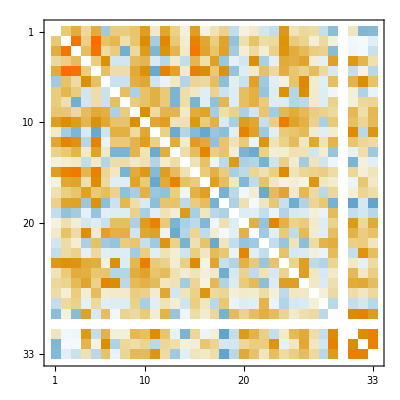

```mathematica
MatrixPlot[binaryCorrMap]
```

```mathematica
binaryCorrMap//Max
```

0.904842

```mathematica
binaryCorrList=Flatten[MapIndexed[f,binaryCorrMap,{2}],1];
```

```mathematica
binaryCorrListSort=Sort[binaryCorrList,#1[[1]]>#2[[1]]&];
```

```mathematica
binaryCorrListSort[[1;;8]]
```

{f[0.904842,{5,2}],f[0.904842,{2,5}],f[0.777778,{5,3}],f[0.777778,{3,5}],f[0.753371,{3,2}],f[0.753371,{2,3}],f[0.714168,{15,3}],f[0.714168,{3,15}]}

交絡 （相関）が強い項目があるはずなので確認。（予想⋆）

(5)「関連度」::(7)「日付」-> 0.78
⋆(5) 「関連度」 :: (20) 「適合性チューニング」-> 0.71
(15)「ビルダー形式GUI」::(30)「V:データプロット」-> 0.65
(7)「日付」::(20)「適合性チューニング」-> 0.58
⋆(14) 「4.ファセット型ナビ」 :: (37)「 N:検索結果リファイン」-> 0.57

```mathematica
headRepRule=Table[{n,n}->1,{n,1,33}]
```

{{1,1}→1,{2,2}→1,{3,3}→1,{4,4}→1,{5,5}→1,{6,6}→1,{7,7}→1,{8,8}→1,{9,9}→1,{10,10}→1,{11,11}→1,{12,12}→1,{13,13}→1,{14,14}→1,{15,15}→1,{16,16}→1,{17,17}→1,{18,18}→1,{19,19}→1,{20,20}→1,{21,21}→1,{22,22}→1,{23,23}→1,{24,24}→1,{25,25}→1,{26,26}→1,{27,27}→1,{28,28}→1,{29,29}→1,{30,30}→1,{31,31}→1,{32,32}→1,{33,33}→1}

```mathematica
headVecs=ReplacePart[Table[0,{33},{33}],headRepRule];
```

## 除外サイトの除去（採用サイトの決定）

除外対象サイト

```mathematica
Map[#[[60]]&,tsvBody]
```

{,1,,1,1,,1,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,1,,,,,,,,,,,,,,}

```mathematica
deleteSite=Position[Map[#[[60]]&,tsvBody],1]
```

{{2},{4},{5},{7},{50}}

採用サイト

```mathematica
(tsvBodySiteD=Delete[tsvBodySite,deleteSite])
```

{国民経済計算  :日本:経済・産業統計,科学技術研究調査  :日本:学術統計,科学研究費補助金　配分結果  :日本:補助金情報,科学技術システムの課題に関する代表的研究者・有識者の意識定点調査  :日本:経済・産業調査報告,全国イノベーション調査(上記と同じサイトに遷移)  :日本:経済・産業調査報告,J-GLOBAL  :日本:学術総合,researchmap  :日本:学術総合,外国人留学生在籍状況調査  :日本:学生支援,大学ポートレート  :日本:大学情報,大学基本情報  :日本:大学情報,CiNii Articles  :日本:学術論文,KAKEN  :日本:補助金情報,厚生労働科学研究成果データベース  :日本:学術総合,賃金構造基本統計調査  :日本:経済・産業統計,品種登録／出願公表データ  :日本:特許等,経済産業省企業活動基本調査  :日本:経済・産業統計,JIP (Japan Industrial Productivity) データベース  :日本:経済・産業統計,成果報告書データベース  :日本:学術総合,知的財産活動調査  :日本:特許等,特許プラットフォーム  :日本:特許等,IIPパテントデータベース  :日本:特許等,指標情報データベース  :日本:学術総合,Orbis  :世界:経済・産業統計,Main Science and Technology Indicators (MSTI)  :世界:経済・産業統計,Research &amp; Development Statistics  :世界:経済・産業統計,WIPO IP Statistics Data Center  :世界:特許等,World Bank Open Data  :世界:経済・産業統計,Espacenet  :欧州:特許等,Eurostat  :欧州:経済・産業統計,eSearch plus  :欧州:特許等,publicdata.eu  :欧州:医療健康,RISIS Datasets  :欧州:学術総合,Data.gov.uk  :英国:学術総合,Science, engineering and technology (SET) Statistics  :英国:学術総合,UNISTATS  :英国:大学情報,Finances of Higher Education Providers  :英国:教育,ONS Gross Domestic Expenditure on Research and Development  :英国:経済・産業統計,英国特許庁データベース  :英国:特許等,CWTS Leiden Ranking  :オランダ:学術統計,University-Industry Research Connections, CWTS  :オランダ:大学のトップページ,ライデン声明(Leiden manifesto for research Metrics)  :オランダ:その他,Bundesbericht Forschung und Innovation / Research and Innovation in Germany  :ドイツ:教育,Daten Potal  :ドイツ:教育,Förderatlas 2015  :ドイツ:補助金情報,DEPATISnet　ドイツ特許庁　特許検索データベース  :ドイツ:特許等,Ausgaben, Einnahmen und Personal der öffentlichen und öffentlich geförderten Einrichtungen für Wissenschaft, Forschung und Entwicklung  :ドイツ:経済・産業統計,Evaluation Procedures  :フランス:教育,data.gouv.fr  :フランス:学術総合,Bases de données gratuites  :フランス:経済・産業統計,Statistiques structurelles d&#8217;entreprises (Alisse)  :フランス:経済・産業統計,Repères et références statistiques sur les enseignements, la formation et la recherche  :フランス:教育・学校統計,Data.gov  :米国:学術総合,National Bureau of Economic Research (NBER)  :米国:経済・産業統計,Academic Institution Profiles  :米国:学術総合,WebCASPAR  :米国:学術総合,Science and Engineering Indicators  :米国:学術統計,FedScope-Federal Human Resources Data  :米国:経済・産業統計,米国特許検索データベース  :米国:特許等,サンフランシスコ宣言(The San Francisco Declaration on Research Assessment (DORA))  :米国:その他}

採用サイトの地域

```mathematica
tsvSiteRegion=Map[StringSplit[#,":"][[2]]&,tsvBodySiteD]
```

{日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,日本,世界,世界,世界,世界,世界,欧州,欧州,欧州,欧州,欧州,英国,英国,英国,英国,英国,英国,オランダ,オランダ,オランダ,ドイツ,ドイツ,ドイツ,ドイツ,ドイツ,フランス,フランス,フランス,フランス,フランス,米国,米国,米国,米国,米国,米国,米国,米国}

```mathematica
tsvSiteRegionUnq=Union[tsvSiteRegion]
```

{世界,日本,欧州,米国,英国,ドイツ,オランダ,フランス}

:地域の色の合成

```mathematica
regionColSch=Map[ColorData["NeonColors"][#]&,Range[0,(tsvSiteRegionUnq//Length)-1]/((tsvSiteRegionUnq//Length)-1)]
```

{RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.828053, 0.26135585714285714, 0.6050392857142857],RGBColor[0.805814, 0.208576, 0.769757]}

::地域の色のルール

```mathematica
regionColSchRl=Apply[Rule,Transpose[{tsvSiteRegionUnq,regionColSch}],{1}]
```

{世界→RGBColor[0.720287, 0.923781, 0.297597],日本→RGBColor[0.7479864285714286, 0.712156, 0.289758],欧州→RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],米国→RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],英国→RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],ドイツ→RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],オランダ→RGBColor[0.828053, 0.26135585714285714, 0.6050392857142857],フランス→RGBColor[0.805814, 0.208576, 0.769757]}

:::地域の色オブジェクト

```mathematica
regionColObj=(tsvSiteRegion/.regionColSchRl)
```

{RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.828053, 0.26135585714285714, 0.6050392857142857],RGBColor[0.828053, 0.26135585714285714, 0.6050392857142857],RGBColor[0.828053, 0.26135585714285714, 0.6050392857142857],RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.805814, 0.208576, 0.769757],RGBColor[0.805814, 0.208576, 0.769757],RGBColor[0.805814, 0.208576, 0.769757],RGBColor[0.805814, 0.208576, 0.769757],RGBColor[0.805814, 0.208576, 0.769757],RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284]}

採用サイトのジャンル

```mathematica
tsvSiteGenre=Map[StringSplit[#,":"][[3]]&,tsvBodySiteD]
```

{経済・産業統計,学術統計,補助金情報,経済・産業調査報告,経済・産業調査報告,学術総合,学術総合,学生支援,大学情報,大学情報,学術論文,補助金情報,学術総合,経済・産業統計,特許等,経済・産業統計,経済・産業統計,学術総合,特許等,特許等,特許等,学術総合,経済・産業統計,経済・産業統計,経済・産業統計,特許等,経済・産業統計,特許等,経済・産業統計,特許等,医療健康,学術総合,学術総合,学術総合,大学情報,教育,経済・産業統計,特許等,学術統計,大学のトップページ,その他,教育,教育,補助金情報,特許等,経済・産業統計,教育,学術総合,経済・産業統計,経済・産業統計,教育・学校統計,学術総合,経済・産業統計,学術総合,学術総合,学術統計,経済・産業統計,特許等,その他}

```mathematica
tsvSiteGenreUnq=Union[tsvSiteGenre]
```

{教育,その他,特許等,医療健康,大学情報,学生支援,学術統計,学術総合,学術論文,補助金情報,教育・学校統計,経済・産業統計,大学のトップページ,経済・産業調査報告}

:ジャンルの色の合成

```mathematica
genreColSch=Map[ColorData["LakeColors"][#]&,Range[0,(tsvSiteGenreUnq//Length)-1]/((tsvSiteGenreUnq//Length)-1)]
```

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.35581715384615387, 0.165903, 0.6171243846153847],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.4806194615384616, 0.3829002, 0.7925491538461538],RGBColor[0.5430206153846154, 0.4913988, 0.8802615384615384],RGBColor[0.5944071538461538, 0.5767085384615385, 0.9101962307692307],RGBColor[0.6402863846153846, 0.6504238461538461, 0.9112420769230769],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.7320448461538461, 0.7978544615384615, 0.9133337692307693],RGBColor[0.7763652307692307, 0.8515780000000001, 0.907878076923077],RGBColor[0.817567923076923, 0.865318, 0.8894193076923077],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.8999733076923077, 0.892798, 0.8525017692307693],RGBColor[0.941176, 0.906538, 0.834043]}

::ジャンルの色のルール

```mathematica
genreColSchRl=Apply[Rule,Transpose[{tsvSiteGenreUnq,genreColSch}],{1}]
```

{教育→RGBColor[0.293416, 0.0574044, 0.529412],その他→RGBColor[0.35581715384615387, 0.165903, 0.6171243846153847],特許等→RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],医療健康→RGBColor[0.4806194615384616, 0.3829002, 0.7925491538461538],大学情報→RGBColor[0.5430206153846154, 0.4913988, 0.8802615384615384],学生支援→RGBColor[0.5944071538461538, 0.5767085384615385, 0.9101962307692307],学術統計→RGBColor[0.6402863846153846, 0.6504238461538461, 0.9112420769230769],学術総合→RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],学術論文→RGBColor[0.7320448461538461, 0.7978544615384615, 0.9133337692307693],補助金情報→RGBColor[0.7763652307692307, 0.8515780000000001, 0.907878076923077],教育・学校統計→RGBColor[0.817567923076923, 0.865318, 0.8894193076923077],経済・産業統計→RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],大学のトップページ→RGBColor[0.8999733076923077, 0.892798, 0.8525017692307693],経済・産業調査報告→RGBColor[0.941176, 0.906538, 0.834043]}

:::ジャンルの色オブジェクト

```mathematica
genreColObj=(tsvSiteGenre/.genreColSchRl)
```

{RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.6402863846153846, 0.6504238461538461, 0.9112420769230769],RGBColor[0.7763652307692307, 0.8515780000000001, 0.907878076923077],RGBColor[0.941176, 0.906538, 0.834043],RGBColor[0.941176, 0.906538, 0.834043],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.5944071538461538, 0.5767085384615385, 0.9101962307692307],RGBColor[0.5430206153846154, 0.4913988, 0.8802615384615384],RGBColor[0.5430206153846154, 0.4913988, 0.8802615384615384],RGBColor[0.7320448461538461, 0.7978544615384615, 0.9133337692307693],RGBColor[0.7763652307692307, 0.8515780000000001, 0.907878076923077],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.4806194615384616, 0.3829002, 0.7925491538461538],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.5430206153846154, 0.4913988, 0.8802615384615384],RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.6402863846153846, 0.6504238461538461, 0.9112420769230769],RGBColor[0.8999733076923077, 0.892798, 0.8525017692307693],RGBColor[0.35581715384615387, 0.165903, 0.6171243846153847],RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.7763652307692307, 0.8515780000000001, 0.907878076923077],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.817567923076923, 0.865318, 0.8894193076923077],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231],RGBColor[0.6402863846153846, 0.6504238461538461, 0.9112420769230769],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692],RGBColor[0.35581715384615387, 0.165903, 0.6171243846153847]}

```mathematica
tsvBodySiteDC=Transpose[{tsvBodySiteD,regionColObj,genreColObj}]
```

{{国民経済計算  :日本:経済・産業統計,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{科学技術研究調査  :日本:学術統計,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.6402863846153846, 0.6504238461538461, 0.9112420769230769]},{科学研究費補助金　配分結果  :日本:補助金情報,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7763652307692307, 0.8515780000000001, 0.907878076923077]},{科学技術システムの課題に関する代表的研究者・有識者の意識定点調査  :日本:経済・産業調査報告,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.941176, 0.906538, 0.834043]},{全国イノベーション調査(上記と同じサイトに遷移)  :日本:経済・産業調査報告,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.941176, 0.906538, 0.834043]},{J-GLOBAL  :日本:学術総合,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{researchmap  :日本:学術総合,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{外国人留学生在籍状況調査  :日本:学生支援,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.5944071538461538, 0.5767085384615385, 0.9101962307692307]},{大学ポートレート  :日本:大学情報,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.5430206153846154, 0.4913988, 0.8802615384615384]},{大学基本情報  :日本:大学情報,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.5430206153846154, 0.4913988, 0.8802615384615384]},{CiNii Articles  :日本:学術論文,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7320448461538461, 0.7978544615384615, 0.9133337692307693]},{KAKEN  :日本:補助金情報,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.7763652307692307, 0.8515780000000001, 0.907878076923077]},{厚生労働科学研究成果データベース  :日本:学術総合,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{賃金構造基本統計調査  :日本:経済・産業統計,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{品種登録／出願公表データ  :日本:特許等,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692]},{経済産業省企業活動基本調査  :日本:経済・産業統計,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{JIP (Japan Industrial Productivity) データベース  :日本:経済・産業統計,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{成果報告書データベース  :日本:学術総合,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{知的財産活動調査  :日本:特許等,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692]},{特許プラットフォーム  :日本:特許等,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692]},{IIPパテントデータベース  :日本:特許等,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692]},{指標情報データベース  :日本:学術総合,RGBColor[0.7479864285714286, 0.712156, 0.289758],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{Orbis  :世界:経済・産業統計,RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{Main Science and Technology Indicators (MSTI)  :世界:経済・産業統計,RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{Research &amp; Development Statistics  :世界:経済・産業統計,RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{WIPO IP Statistics Data Center  :世界:特許等,RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692]},{World Bank Open Data  :世界:経済・産業統計,RGBColor[0.720287, 0.923781, 0.297597],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{Espacenet  :欧州:特許等,RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692]},{Eurostat  :欧州:経済・産業統計,RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{eSearch plus  :欧州:特許等,RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692]},{publicdata.eu  :欧州:医療健康,RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.4806194615384616, 0.3829002, 0.7925491538461538]},{RISIS Datasets  :欧州:学術総合,RGBColor[0.7756858571428572, 0.5005305714285714, 0.28191900000000003],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{Data.gov.uk  :英国:学術総合,RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{Science, engineering and technology (SET) Statistics  :英国:学術総合,RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{UNISTATS  :英国:大学情報,RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.5430206153846154, 0.4913988, 0.8802615384615384]},{Finances of Higher Education Providers  :英国:教育,RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.293416, 0.0574044, 0.529412]},{ONS Gross Domestic Expenditure on Research and Development  :英国:経済・産業統計,RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{英国特許庁データベース  :英国:特許等,RGBColor[0.8580941428571429, 0.3168661428571428, 0.29074814285714284],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692]},{CWTS Leiden Ranking  :オランダ:学術統計,RGBColor[0.828053, 0.26135585714285714, 0.6050392857142857],RGBColor[0.6402863846153846, 0.6504238461538461, 0.9112420769230769]},{University-Industry Research Connections, CWTS  :オランダ:大学のトップページ,RGBColor[0.828053, 0.26135585714285714, 0.6050392857142857],RGBColor[0.8999733076923077, 0.892798, 0.8525017692307693]},{ライデン声明(Leiden manifesto for research Metrics)  :オランダ:その他,RGBColor[0.828053, 0.26135585714285714, 0.6050392857142857],RGBColor[0.35581715384615387, 0.165903, 0.6171243846153847]},{Bundesbericht Forschung und Innovation / Research and Innovation in Germany  :ドイツ:教育,RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.293416, 0.0574044, 0.529412]},{Daten Potal  :ドイツ:教育,RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.293416, 0.0574044, 0.529412]},{Förderatlas 2015  :ドイツ:補助金情報,RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.7763652307692307, 0.8515780000000001, 0.907878076923077]},{DEPATISnet　ドイツ特許庁　特許検索データベース  :ドイツ:特許等,RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692]},{Ausgaben, Einnahmen und Personal der öffentlichen und öffentlich geförderten Einrichtungen für Wissenschaft, Forschung und Entwicklung  :ドイツ:経済・産業統計,RGBColor[0.850292, 0.3141357142857143, 0.44032257142857145],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{Evaluation Procedures  :フランス:教育,RGBColor[0.805814, 0.208576, 0.769757],RGBColor[0.293416, 0.0574044, 0.529412]},{data.gouv.fr  :フランス:学術総合,RGBColor[0.805814, 0.208576, 0.769757],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{Bases de données gratuites  :フランス:経済・産業統計,RGBColor[0.805814, 0.208576, 0.769757],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{Statistiques structurelles d&#8217;entreprises (Alisse)  :フランス:経済・産業統計,RGBColor[0.805814, 0.208576, 0.769757],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{Repères et références statistiques sur les enseignements, la formation et la recherche  :フランス:教育・学校統計,RGBColor[0.805814, 0.208576, 0.769757],RGBColor[0.817567923076923, 0.865318, 0.8894193076923077]},{Data.gov  :米国:学術総合,RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{National Bureau of Economic Research (NBER)  :米国:経済・産業統計,RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{Academic Institution Profiles  :米国:学術総合,RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{WebCASPAR  :米国:学術総合,RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.6861656153846154, 0.7241391538461539, 0.9122879230769231]},{Science and Engineering Indicators  :米国:学術統計,RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.6402863846153846, 0.6504238461538461, 0.9112420769230769]},{FedScope-Federal Human Resources Data  :米国:経済・産業統計,RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.8587706153846154, 0.879058, 0.8709605384615384]},{米国特許検索データベース  :米国:特許等,RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.4182183076923077, 0.2744016, 0.7048367692307692]},{サンフランシスコ宣言(The San Francisco Declaration on Research Assessment (DORA))  :米国:その他,RGBColor[0.8191944285714285, 0.334589, 0.25419514285714284],RGBColor[0.35581715384615387, 0.165903, 0.6171243846153847]}}

採用サイトID

```mathematica
(tsvBodyIDD=Delete[tsvBodyID,deleteSite])
```

{1,4,7,15,16,18,19,20,21,22,23,24,25,26,27,28,32,35,36,37,38,42,43,46,48,53,54,55,57,58,59,60,61,62,63,64,66,67,68,69,70,71,72,73,74,77,82,83,84,85,86,90,91,93,103,104,105,106,108}

採用項目と採用サイトによる行列

```mathematica
(tsvBinaryBodyZDropD=Delete[tsvBinaryBodyZDrop,deleteSite])//Dimensions
```

{59,33}

## 分布の確認

```mathematica
siteScore=Map[Tr,tsvBinaryBodyZDropD]
```

{12,11,13,5,5,15,6,13,13,3,15,18,8,13,9,11,13,13,12,11,10,2,5,14,14,10,10,9,15,9,3,6,19,12,7,4,12,9,14,7,3,9,8,15,4,16,14,18,15,13,4,20,12,6,14,5,10,6,6}

サイトのスコアのヒストグラム

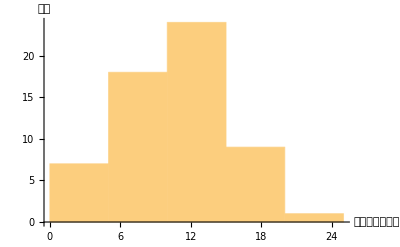

```mathematica
Histogram[siteScore,5,AxesLabel->{"サイトのスコア","頻度"}]
```

サイトのスコア

```mathematica
siteScoreTop=Sort[({tsvBodySiteD,siteScore}//Transpose),#1[[2]]>#2[[2]]&]
```

{{Data.gov  :米国:学術総合,20},{Data.gov.uk  :英国:学術総合,19},{data.gouv.fr  :フランス:学術総合,18},{KAKEN  :日本:補助金情報,18},{Ausgaben, Einnahmen und Personal der öffentlichen und öffentlich geförderten Einrichtungen für Wissenschaft, Forschung und Entwicklung  :ドイツ:経済・産業統計,16},{Bases de données gratuites  :フランス:経済・産業統計,15},{Förderatlas 2015  :ドイツ:補助金情報,15},{Eurostat  :欧州:経済・産業統計,15},{CiNii Articles  :日本:学術論文,15},{J-GLOBAL  :日本:学術総合,15},{WebCASPAR  :米国:学術総合,14},{Evaluation Procedures  :フランス:教育,14},{CWTS Leiden Ranking  :オランダ:学術統計,14},{Research &amp; Development Statistics  :世界:経済・産業統計,14},{Main Science and Technology Indicators (MSTI)  :世界:経済・産業統計,14},{Statistiques structurelles d&#8217;entreprises (Alisse)  :フランス:経済・産業統計,13},{成果報告書データベース  :日本:学術総合,13},{JIP (Japan Industrial Productivity) データベース  :日本:経済・産業統計,13},{賃金構造基本統計調査  :日本:経済・産業統計,13},{大学ポートレート  :日本:大学情報,13},{外国人留学生在籍状況調査  :日本:学生支援,13},{科学研究費補助金　配分結果  :日本:補助金情報,13},{National Bureau of Economic Research (NBER)  :米国:経済・産業統計,12},{ONS Gross Domestic Expenditure on Research and Development  :英国:経済・産業統計,12},{Science, engineering and technology (SET) Statistics  :英国:学術総合,12},{知的財産活動調査  :日本:特許等,12},{国民経済計算  :日本:経済・産業統計,12},{特許プラットフォーム  :日本:特許等,11},{経済産業省企業活動基本調査  :日本:経済・産業統計,11},{科学技術研究調査  :日本:学術統計,11},{FedScope-Federal Human Resources Data  :米国:経済・産業統計,10},{World Bank Open Data  :世界:経済・産業統計,10},{WIPO IP Statistics Data Center  :世界:特許等,10},{IIPパテントデータベース  :日本:特許等,10},{Bundesbericht Forschung und Innovation / Research and Innovation in Germany  :ドイツ:教育,9},{英国特許庁データベース  :英国:特許等,9},{eSearch plus  :欧州:特許等,9},{Espacenet  :欧州:特許等,9},{品種登録／出願公表データ  :日本:特許等,9},{Daten Potal  :ドイツ:教育,8},{厚生労働科学研究成果データベース  :日本:学術総合,8},{University-Industry Research Connections, CWTS  :オランダ:大学のトップページ,7},{UNISTATS  :英国:大学情報,7},{サンフランシスコ宣言(The San Francisco Declaration on Research Assessment (DORA))  :米国:その他,6},{米国特許検索データベース  :米国:特許等,6},{Academic Institution Profiles  :米国:学術総合,6},{RISIS Datasets  :欧州:学術総合,6},{researchmap  :日本:学術総合,6},{Science and Engineering Indicators  :米国:学術統計,5},{Orbis  :世界:経済・産業統計,5},{全国イノベーション調査(上記と同じサイトに遷移)  :日本:経済・産業調査報告,5},{科学技術システムの課題に関する代表的研究者・有識者の意識定点調査  :日本:経済・産業調査報告,5},{Repères et références statistiques sur les enseignements, la formation et la recherche  :フランス:教育・学校統計,4},{DEPATISnet　ドイツ特許庁　特許検索データベース  :ドイツ:特許等,4},{Finances of Higher Education Providers  :英国:教育,4},{ライデン声明(Leiden manifesto for research Metrics)  :オランダ:その他,3},{publicdata.eu  :欧州:医療健康,3},{大学基本情報  :日本:大学情報,3},{指標情報データベース  :日本:学術総合,2}}

```mathematica
siteScoreTop[[1;;10]]//TableForm
```

Data.gov  :米国:学術総合 | 20
Data.gov.uk  :英国:学術総合 | 19
data.gouv.fr  :フランス:学術総合 | 18
KAKEN  :日本:補助金情報 | 18
Ausgaben, Einnahmen und Personal der öffentlichen und öffentlich geförderten Einrichtungen für Wissenschaft, Forschung und Entwicklung  :ドイツ:経済・産業統計 | 16
Bases de données gratuites  :フランス:経済・産業統計 | 15
Förderatlas 2015  :ドイツ:補助金情報 | 15
Eurostat  :欧州:経済・産業統計 | 15
CiNii Articles  :日本:学術論文 | 15
J-GLOBAL  :日本:学術総合 | 15

```mathematica
Position[tsvBodySiteD,"Data.gov"]
```

{}

```mathematica
Position[tsvBodySiteD,"Data.gov.uk"]
```

{}

```mathematica
Position[tsvBodySiteD,"data.gouv.fr"]
```

{}

```mathematica
Position[tsvBodySiteD,"KAKEN"]
```

{}

```mathematica
siteScoreTopPos={{52},{33},{48},{12}}
```

{{52},{33},{48},{12}}

Top4で違いのある項目

```mathematica
siteScoreTopVec=tsvBinaryBodyZDropD[[Flatten[siteScoreTopPos]]]
```

{{0,1,1,1,1,1,0,0,1,1,0,0,1,0,1,1,1,0,0,0,1,0,0,1,0,1,1,0,1,1,1,1,1},{0,1,1,0,1,1,0,0,1,1,0,1,1,0,1,1,1,0,0,0,0,0,0,0,1,1,1,0,1,1,1,1,1},{1,1,1,1,1,0,0,0,1,1,0,1,1,0,1,1,1,0,0,0,0,0,0,1,1,0,1,0,1,1,1,0,0},{0,1,1,0,1,0,0,0,0,1,0,1,1,0,1,1,1,1,0,1,0,0,1,1,0,0,1,0,1,1,0,1,1}}

```mathematica
Count[Map[Tr,Transpose[siteScoreTopVec]],x_/;x>0&&x<4]
```

15

```mathematica
{Range[33],tsvEvalHeadDrop,Map[Tr,Transpose[siteScoreTopVec]]}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33
**サジェスト | 2.ベストファースト = O:ソート | * 関連度 | * 人気度 | * 日付 | * フォーマット（ソースの） | * 多様性（多様性(表現の多様性の吸収など)アルゴリズム） | **スコア | **エンジン（マルチエンジン） | 4. ファセット型ナビ = ファセット型ナビ | L:ビルダー形式GUI | 5.詳細検索 = K:詳細検索 | J:検索box | X:login機能 | **適合性のチューニング | 7.ページネーション = ページネーション | Q:全件表示 | **ハイライト | **クラスタリング | V:データプロット | U:マップ | S:サムネイル | W:ロケータ/スライダ等、GUIによる指定 | N:検索結果リファイン | **レコメン | **トピック | 11. NISTEPサービスにあるが本書にない項目（空項目） | R:バリアフリー | P:ダウンロード | M:検索対象のタイプ | T:ダウンロードのデータ形式 | Z1:API | Z:その他
1 | 4 | 4 | 2 | 4 | 2 | 0 | 0 | 3 | 4 | 0 | 3 | 4 | 0 | 4 | 4 | 4 | 1 | 0 | 1 | 1 | 0 | 1 | 3 | 2 | 2 | 4 | 0 | 4 | 4 | 3 | 3 | 3

```mathematica
Position[Map[Tr,Transpose[siteScoreTopVec]],1]
```

{{1},{18},{20},{21},{23}}

稀な項目

```mathematica
(hitCount=Map[Tr,tsvBinaryBodyZDropD//Transpose])
```

{14,36,27,2,34,3,4,3,27,25,3,41,55,8,25,47,17,21,1,4,3,11,1,20,5,5,58,1,15,59,12,5,16}

```mathematica
Position[hitCount,1]
```

{{19},{23},{28}}

```mathematica
hitCountTop=Sort[{hitCount,tsvEvalHeadDrop}//Transpose,#1[[1]]<#2[[1]]&]
```

{{1,R:バリアフリー},{1,W:ロケータ/スライダ等、GUIによる指定},{1,**クラスタリング},{2,* 人気度},{3,U:マップ},{3,L:ビルダー形式GUI},{3,**スコア},{3,* フォーマット（ソースの）},{4,V:データプロット},{4,* 多様性（多様性(表現の多様性の吸収など)アルゴリズム）},{5,Z1:API},{5,**トピック},{5,**レコメン},{8,X:login機能},{11,S:サムネイル},{12,T:ダウンロードのデータ形式},{14,**サジェスト},{15,P:ダウンロード},{16,Z:その他},{17,Q:全件表示},{20,N:検索結果リファイン},{21,**ハイライト},{25,**適合性のチューニング},{25,4. ファセット型ナビ = ファセット型ナビ},{27,**エンジン（マルチエンジン）},{27,* 関連度},{34,* 日付},{36,2.ベストファースト = O:ソート},{41,5.詳細検索 = K:詳細検索},{47,7.ページネーション = ページネーション},{55,J:検索box},{58,11. NISTEPサービスにあるが本書にない項目（空項目）},{59,M:検索対象のタイプ}}

```mathematica
hitCountTop[[1;;3]]//TableForm
```

1 | R:バリアフリー
1 | W:ロケータ/スライダ等、GUIによる指定
1 | **クラスタリング

## 階層クラスタリング(2)

```mathematica
tsvBodySiteD//Dimensions
```

{59}

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
tx=Map[Graphics[{Text[Style[#,6],{0,0},{0,0},{0,-1}]}]&,tsvBodySiteD];
```

```mathematica
tx=Map[Graphics[{Text[Style[#,6],{0,0},{0,0},{0,-1}],Point[{0,1.3}]}]&,tsvBodySiteD];
```

```mathematica
tx=Map[Graphics[{Text[Style[#[[1]],6],{0,0},{0,0},{0,-1}],#[[2]],Point[{0,1.7}],#[[3]],Point[{0,1.6}]}]&,tsvBodySiteDC];
```

Agglomerate::ties: 40 ties have been detected; reordering input may produce a different result.

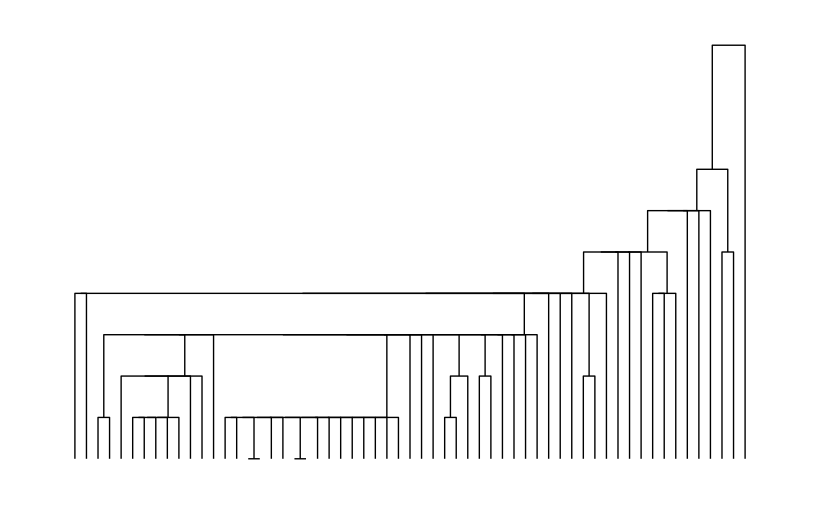
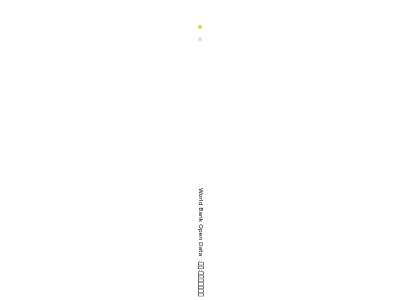
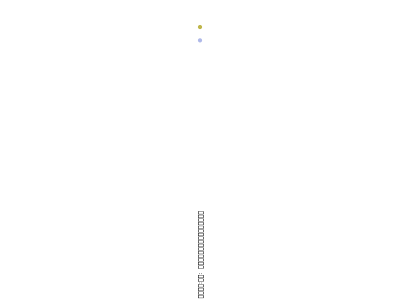
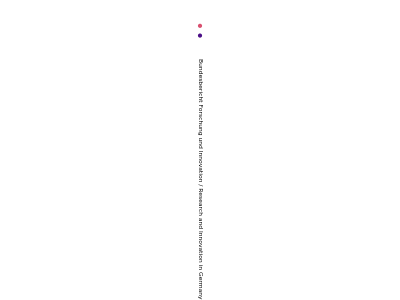
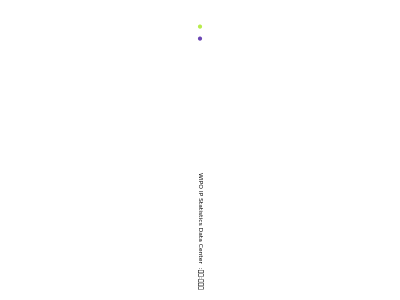
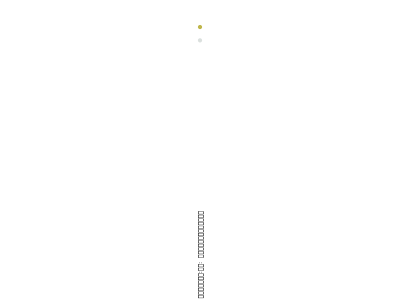
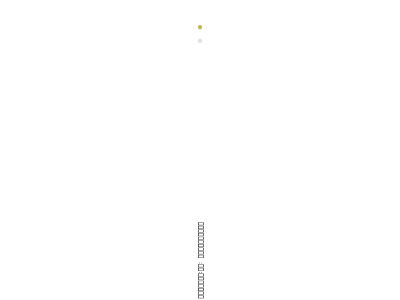
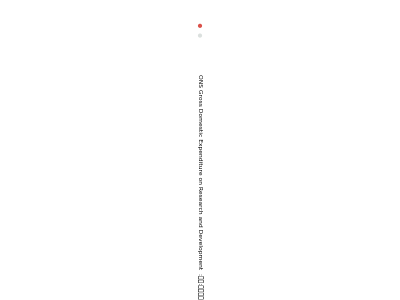
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
dp=DendrogramPlot[tsvBinaryBodyZDropD,LeafLabels->tx]
```

```mathematica
dp[[1]][[3]]
```

{Text[-Graphics-,Offset[{0,-4},{1,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{2,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{3,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{4,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{5,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{6,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{7,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{8,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{9,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{10,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{11,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{12,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{13,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{14,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{15,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{16,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{17,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{18,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{19,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{20,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{21,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{22,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{23,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{24,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{25,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{26,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{27,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{28,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{29,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{30,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{31,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{32,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{33,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{34,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{35,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{36,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{37,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{38,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{39,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{40,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{41,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{42,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{43,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{44,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{45,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{46,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{47,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{48,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{49,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{50,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{51,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{52,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{53,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{54,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{55,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{56,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{57,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{58,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{59,0}],{0,1}]}

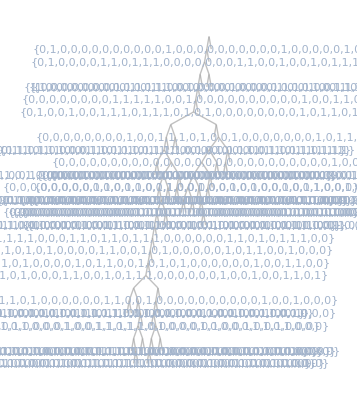

```mathematica
ClusteringTree[tsvBinaryBodyZDropD]
```

## 階層クラスタリング*

```mathematica
tsvBodySiteD//Dimensions
```

{59}

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
tx=Map[Graphics[{Text[Style[#,6],{0,0},{0,0},{0,-1}]}]&,tsvBodySiteD];
```

```mathematica
tx=Map[Graphics[{Text[Style[#,6],{0,0},{0,0},{0,-1}],Point[{0,1.3}]}]&,tsvBodySiteD];
```

Agglomerate::ties: 40 ties have been detected; reordering input may produce a different result.

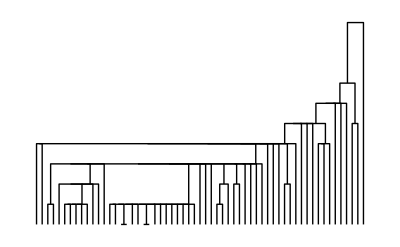
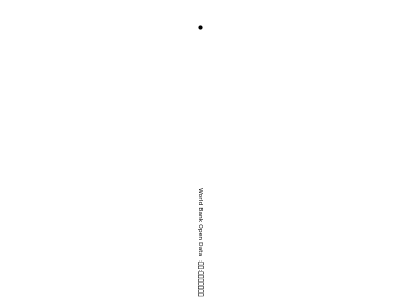
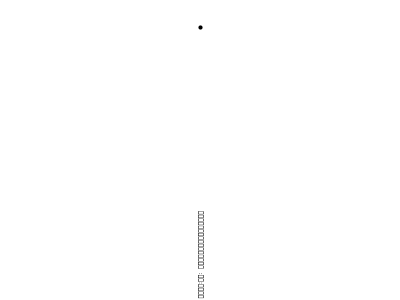
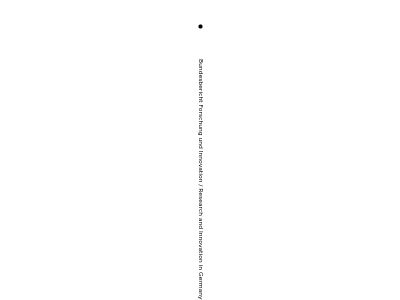
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
dp=DendrogramPlot[tsvBinaryBodyZDropD,LeafLabels->tx]
```

```mathematica
dp[[1]][[3]]
```

{Text[-Graphics-,Offset[{0,-4},{1,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{2,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{3,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{4,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{5,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{6,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{7,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{8,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{9,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{10,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{11,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{12,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{13,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{14,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{15,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{16,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{17,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{18,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{19,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{20,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{21,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{22,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{23,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{24,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{25,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{26,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{27,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{28,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{29,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{30,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{31,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{32,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{33,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{34,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{35,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{36,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{37,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{38,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{39,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{40,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{41,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{42,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{43,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{44,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{45,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{46,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{47,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{48,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{49,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{50,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{51,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{52,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{53,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{54,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{55,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{56,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{57,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{58,0}],{0,1}],Text[-Graphics-,Offset[{0,-4},{59,0}],{0,1}]}

```mathematica
ClusteringTree[tsvBinaryBodyZDropD]
```

-Graphics-

## サービスの空間配置の確認(PCA)

### 規格化なし；分散法

```mathematica
(pca=PrincipalComponents[N[tsvBinaryBodyZDropD]])//Dimensions
```

{59,33}

クラスタリング用データのExport

```mathematica
Export["zeroDrop_.sv",matTokmeansSV[tsvBinaryBodyZDropD],"Text"]
```

zeroDrop_.sv

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,pca]},Frame->True,PlotLabel->"規格化なし"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,pca]}]
```

-Graphics3D-

### 規格化なし；相関法*

```mathematica
(pcaC=PrincipalComponents[N[tsvBinaryBodyZDropD],Method->"Correlation"])//Dimensions
```

{59,33}

```mathematica
(txpos=Map[#[[Range[2]]]&,pcaC])//Length
```

59

```mathematica
(tx=tsvBodySiteD)//Length
```

59

```mathematica
gtxt=Table[Text[tx[[n]],txpos[[n]]+{0,-0.13}],{n,Length[tx]}];
```

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,pcaC],gtxt},Frame->True,PlotLabel->"規格化なし、相関法"]
```

-Graphics-

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,pcaC]},Frame->True,PlotLabel->"規格化なし、相関法"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,pcaC]}]
```

-Graphics3D-

### カウント規格化；分散法

```mathematica
(cnpca=PrincipalComponents[tsvBinaryBodyZDropDCN=Transpose[Map[countNormal,Transpose[N[tsvBinaryBodyZDropD]]]]])//Dimensions
```

{59,33}

クラスタリング用データのExport

```mathematica
Export["zeroDrop_CN.sv",matTokmeansSV[tsvBinaryBodyZDropDCN],"Text"]
```

zeroDrop_CN.sv

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,cnpca]},Frame->True, PlotLabel->"カウント規格化"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,cnpca]}]
```

-Graphics3D-

### カウント規格化；相関法

```mathematica
(cnpcaC=PrincipalComponents[Transpose[Map[countNormal,Transpose[N[tsvBinaryBodyZDropD]]]],Method->"Correlation"])//Dimensions
```

{59,33}

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,cnpcaC]},Frame->True,PlotLabel->"カウント規格化、相関法"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,cnpcaC]}]
```

-Graphics3D-

### ノルム規格化；分散法

```mathematica
(npca=PrincipalComponents[tsvBinaryBodyZDropDNN=Transpose[Map[Normalize,Transpose[N[tsvBinaryBodyZDropD]]]]])//Dimensions
```

{59,33}

クラスタリング用データのExport

```mathematica
Export["zeroDrop_NN.sv",matTokmeansSV[tsvBinaryBodyZDropDNN],"Text"]
```

zeroDrop_NN.sv

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,npca]},Frame->True,PlotLabel->"ノルム規格化"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,npca]}]
```

-Graphics3D-

### ノルム規格化；相関法

```mathematica
(npcaC=PrincipalComponents[Transpose[Map[Normalize,Transpose[N[tsvBinaryBodyZDropD]]]],Method->"Correlation"])//Dimensions
```

{59,33}

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,npcaC]},Frame->True,PlotLabel->"ノルム規格化、相関法"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,npcaC]}]
```

-Graphics3D-

## サービスの空間配置の確認(LLE)

### 規格化なし

```mathematica
(lle2D=DimensionReduce[N[tsvBinaryBodyZDropD],2,Method->"LLE"])//Dimensions
```

{59,2}

```mathematica
(lle3D=DimensionReduce[N[tsvBinaryBodyZDropD],3,Method->"LLE"])//Dimensions
```

{59,3}

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,lle2D]},Frame->True,PlotLabel->"規格化なし"]
```

-Graphics-

```mathematica
Graphics3D[{PointSize[0.02],Map[Point[#[[Range[1,3]]]]&,lle3D]}]
```

-Graphics3D-

## 項目空間にマップしたサービスの分布

### 規格化なし；PCA:相関法

```mathematica
(name=Join[tsvEvalHeadDrop,tsvBodySiteD])//Length
```

92

```mathematica
Dimensions[jointBinary=Join[headVecs,tsvBinaryBodyZDropD]]
```

{92,33}

```mathematica
JBPCA=PrincipalComponents[jointBinary//N,Method->"Correlation"];
```

```mathematica
(txpos=Map[#[[Range[2]]]&,JBPCA])//Length
```

92

```mathematica
tx=name;
```

```mathematica
gtxt=Table[Text[tx[[n]],txpos[[n]]+{0,-0.13}],{n,Length[tx]}];
```

```mathematica
Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,JBPCA],gtxt},Frame->True,PlotLabel->"規格化なし、相関法"]
```

-Graphics-

### ノルム規格化；PCA相関法

```mathematica
(name=Join[tsvEvalHeadDrop,tsvBodySiteD])//Length
```

92

```mathematica
Dimensions[jointBinary=Join[headVecs,Map[Normalize,tsvBinaryBodyZDropD]]]
```

{92,33}

```mathematica
JBPCA=PrincipalComponents[jointBinary//N,Method->"Correlation"];
```

```mathematica
(txpos=Map[#[[Range[2]]]&,JBPCA])//Length
```

92

```mathematica
tx=name;
```

```mathematica
gtxt=Table[Text[tx[[n]],txpos[[n]]+{0,-0.13}],{n,Length[tx]}];
```

```mathematica
attPlot["PCA:Norm"]=Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,JBPCA],gtxt},Frame->True,PlotLabel->"規格化、PCA相関法",ImageSize->{1300,1100}]
```

-Graphics-

```mathematica
Export["AttPlot-PCA_norm.png",attPlot["PCA:Norm"]]
```

AttPlot-PCA_norm.png

### ノルム規格化；MDS

```mathematica
(name=Join[tsvEvalHeadDrop,tsvBodySiteD])//Length
```

92

```mathematica
Dimensions[jointBinary=Join[headVecs,Map[Normalize,tsvBinaryBodyZDropD]]]
```

{92,33}

```mathematica
JBMDS=DimensionReduce[jointBinary//N,2,Method->"MultidimensionalScaling"];
```

```mathematica
(txpos=Map[#[[Range[2]]]&,JBMDS])//Length
```

92

```mathematica
tx=name;
```

```mathematica
gtxt=Table[Text[tx[[n]],txpos[[n]]+{0,-0.03}],{n,Length[tx]}];
```

```mathematica
attPlot["MDS:Norm"]=Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,JBMDS],gtxt},Frame->True,PlotLabel->"規格化、MDS",ImageSize->{1300,1100}]
```

-Graphics-

```mathematica
Export["AttPlot-MDS_norm.png",attPlot["MDS:Norm"]]
```

AttPlot-MDS_norm.png

### ノルム規格化；TSNE

```mathematica
(name=Join[tsvEvalHeadDrop,tsvBodySiteD])//Length
```

92

```mathematica
Dimensions[jointBinary=Join[headVecs,Map[Normalize,tsvBinaryBodyZDropD]]]
```

{92,33}

```mathematica
JBTSNE=DimensionReduce[jointBinary//N,2,Method->"TSNE"];
```

```mathematica
(txpos=Map[#[[Range[2]]]&,JBTSNE])//Length
```

92

```mathematica
tx=name;
```

```mathematica
gtxt=Table[Text[tx[[n]],txpos[[n]]+{0,-0.16}],{n,Length[tx]}];
```

```mathematica
attPlot["TSNE:Norm"]=Graphics[{PointSize[0.02],Map[Point[#[[Range[1,2]]]]&,JBTSNE],gtxt},Frame->True,PlotLabel->"規格化、TSNE",ImageSize->{1300,1100}]
```

-Graphics-

```mathematica
Export["AttPlot-TSNE_norm.png",attPlot["TSNE:Norm"]]
```

AttPlot-TSNE_norm.png

## k-meansクラスタリング結果の確認

```mathematica
baseName={"zeroDrop_","zeroDrop_CN","zeroDrop_NN"}
```

{zeroDrop_,zeroDrop_CN,zeroDrop_NN}

```mathematica
count={"5","10","15","20","25","30","35","40","45","50"}
```

{5,10,15,20,25,30,35,40,45,50}

```mathematica
dist={"_cos","_ecl"}
```

{_cos,_ecl}

```mathematica
FileNames["*log"]
```

{}

```mathematica
FileNames[RegularExpression["zeroDrop__C_.*_ecl.log"]]
```

{}

```mathematica
zdf=.
```

```mathematica
zdf[baseName[[1]]][dist[[1]]]=Table[baseName[[1]]<>"_C_"<>t<>dist[[1]]<>".log",{t,count}]
```

{zeroDrop__C_5_cos.log,zeroDrop__C_10_cos.log,zeroDrop__C_15_cos.log,zeroDrop__C_20_cos.log,zeroDrop__C_25_cos.log,zeroDrop__C_30_cos.log,zeroDrop__C_35_cos.log,zeroDrop__C_40_cos.log,zeroDrop__C_45_cos.log,zeroDrop__C_50_cos.log}

```mathematica
Do[zdf[baseName[[b]]][dist[[d]]]=Table[baseName[[b]]<>"_C_"<>t<>dist[[d]]<>".log",{t,count}],{b,3},{d,2}]
```

```mathematica
zdf[baseName[[2]]][dist[[2]]]
```

{zeroDrop_CN_C_5_ecl.log,zeroDrop_CN_C_10_ecl.log,zeroDrop_CN_C_15_ecl.log,zeroDrop_CN_C_20_ecl.log,zeroDrop_CN_C_25_ecl.log,zeroDrop_CN_C_30_ecl.log,zeroDrop_CN_C_35_ecl.log,zeroDrop_CN_C_40_ecl.log,zeroDrop_CN_C_45_ecl.log,zeroDrop_CN_C_50_ecl.log}

```mathematica
zdfl=.
```

```mathematica
Do[zdfl[baseName[[b]]][dist[[d]]]=Table[Get[(zdf[baseName[[b]]][dist[[d]]][[n]])],{n,Length[count]}],{b,3},{d,2}]
```

Get::noopen: zeroDrop__C_5_cos.logを開くことができません．

Get::noopen: zeroDrop__C_10_cos.logを開くことができません．

Get::noopen: zeroDrop__C_15_cos.logを開くことができません．

General::stop: この計算中に，Get::noopenのこれ以上の出力は表示されません．

```mathematica
Table[{baseName[[b]],dist[[d]]},{b,3},{d,2}]
```

{{{zeroDrop_,_cos},{zeroDrop_,_ecl}},{{zeroDrop_CN,_cos},{zeroDrop_CN,_ecl}},{{zeroDrop_NN,_cos},{zeroDrop_NN,_ecl}}}

```mathematica
Transpose[Map[{#[[3,2,2]],#[[3,2,3]]}&,zdfl[baseName[[1]]][dist[[1]]]]]
```

Part::partd: 部分指定$Failed⟦3,2,2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed⟦3,2,3⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed⟦3,2,2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}}

```mathematica
pltTbl=Table[Transpose[Map[{#[[3,2,2]],#[[3,2,3]]}&,zdfl[baseName[[b]]][dist[[d]]]]],{b,3},{d,2}]
```

Part::partd: 部分指定$Failed⟦3,2,2⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed⟦3,2,3⟧の長さはオブジェクトの深さを超えています．

Part::partd: 部分指定$Failed⟦3,2,2⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

{{{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}},{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}}},{{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}},{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}}},{{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}},{{$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧,$Failed⟦3,2,2⟧},{$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧,$Failed⟦3,2,3⟧}}}}

```mathematica
Table[ListPlot[pltTbl[[b,d]],PlotLabel->baseName[[b]]<>dist[[d]],AxesLabel->{"step",None}, Joined->True],{b,3},{d,2}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[ListPlot[pltTbl[[b,d]],AxesLabel->{"step",None}, Joined->True],{b,3},{d,2}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Table[ListPlot[pltTbl[[b,d]],Joined->True],{b,3},{d,2}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}